```mathematica
Exit
```

## Initialization

### Imports

#### Import SIAF

```mathematica
siafLocation=FileNameJoin[{NotebookDirectory[],"MIRI_SIAF.xml"}];
```

```mathematica
Import["/Users/bnickson/GitHub/Gen_PSFMASK_ref_files/MIRI_SIAF.xml"];
```

```mathematica
miriSiafXML=Import[siafLocation];
siafEntriesPre=Cases[miriSiafXML,XMLElement["SiafEntry",_,x_]->x,Infinity];
siafEntriesPre2=Flatten[Cases[#,XMLElement[x_,_,{y_}]->{x->y},{1}]]&/@siafEntriesPre;
instrums="InstrName"/.siafEntriesPre2;
apNames="AperName"/.siafEntriesPre2;
siafEntriesPre3=Table[apNames[[k]]-> Complement[siafEntriesPre2[[k]],{"InstrName"->instrums[[k]],"AperName"->apNames[[k]]}],{k,Length@siafEntriesPre2}];
```

#### Import backlit image of MIRI FULL array for reference

```mathematica
ilumImDir=FileNameJoin[{NotebookDirectory[],"f1065c.fits"}];
```

```mathematica
ilumIm=First@Import[ilumImDir,"RawData"];
ArrayPlot[ilumIm,DataReversed->True, PlotLabel->Style["Backlit MIRI FULL array image",18] ]
```

-Graphics-

#### Import flat files

```mathematica
fileDir=NotebookDirectory[]<>"flat_files/";
flatData=Import[fileDir<>#,"RawData"]&/@{"jwst_miri_flat_0413.fits","jwst_miri_flat_0424.fits","jwst_miri_flat_0457.fits","jwst_miri_flat_0407.fits"};
```

#### Import old psfmask reference files

```mathematica
tmpMaskDir=NotebookDirectory[]<>"psf_masks_old/";
psf1065mask=Import[tmpMaskDir<>"jwst_miri_psfmask_0001.fits","RawData"][[2]];
psf1550mask=Import[tmpMaskDir<>"jwst_miri_psfmask_0002.fits","RawData"][[2]];
psf1140mask=Import[tmpMaskDir<>"jwst_miri_psfmask_0003.fits","RawData"][[2]];
psfLYOTmask=Import[tmpMaskDir<>"jwst_miri_psfmask_0004.fits","RawData"][[2]];
refs={psf1065mask,psf1550mask,psf1140mask,psfLYOTmask};
```

### Definitions

Here we define the apertures and their IWAs

```mathematica
apers={"MIRIM_MASK1065","MIRIM_MASK1550","MIRIM_MASK1140","MIRIM_MASKLYOT"};
IWAS={0.33,0.49,0.36,2.16};
pixelScale=0.11;
kass=Association@Thread[apers->Range@Length@apers];

(*Extract the name of the mask from aperture name, just used for plot annotations *)
masks = StringDelete[apers,"MIRIM_"]
```

{MASK1065,MASK1550,MASK1140,MASKLYOT}

Here we define the function used to create the aperture

```mathematica
Clear@MakeAperture
MakeAperture=Compile[{R1,m,n},Module[{i,j,n0},n0=n/2+1;
N[Table[If[Sqrt[(i-n0)^2+(j-n0)^2]<R1,1,0],{i,m},{j,n}]]]];
```

```mathematica
submat[mat_,p1_,p2_]:=mat[[p1[[2]];;p2[[2]],p1[[1]];;p2[[1]]]]
```

Here we cut out the coronagraphic subarrays from the backlit image of the MIRI FULL array, using the dimensions for each subarray from SIAF.
We will later use these images to check the mask files.

```mathematica
apers={"MIRIM_MASK1065","MIRIM_MASK1550","MIRIM_MASK1140","MIRIM_MASKLYOT"};
keysofInterest={"XSciSize","YSciSize"};
keysLocation={"XDetRef","YDetRef","XSciRef","YSciRef"};
```

```mathematica
illumIms=Table[
aperName=apers[[k]];
siafEntry=aperName/.siafEntriesPre3;
{xdims,ydims}=Map[ToExpression,keysofInterest/.siafEntry];
{xDetRef,yDetRef,xSciRef,ySciRef}=ToExpression/@(keysLocation/.siafEntry);
firstPix=Round[{xDetRef-xSciRef+1,yDetRef-ySciRef+1}];
point2=(firstPix+{xdims,ydims})-1;
submat[ilumIm,firstPix,point2]
,{k,Length@apers}];
```

```mathematica
Row@{ArrayPlot[illumIms[[1]],DataReversed->True,PlotLabel->Style["Backlit "masks[[1]]" Subarray",18],ImageSize->300],
ArrayPlot[illumIms[[2]],DataReversed->True,PlotLabel->Style["Backlit "masks[[2]]" Subarray",18],ImageSize->300],
ArrayPlot[illumIms[[3]],DataReversed->True,PlotLabel->Style["Backlit "masks[[3]]" Subarray",18],ImageSize->300],
ArrayPlot[illumIms[[4]],DataReversed->True,PlotLabel->Style["Backlit "masks[[4]]" Subarray",18],ImageSize->300]}
```

-Graphics--Graphics--Graphics--Graphics-

center 1065 = 121, 115

```mathematica
(*Location where the new psfmask files will be written*)
expDirPre=NotebookDirectory[]<>"psf_masks_new/mathematica_out/"
```

/Users/bnickson/GitHub/Gen_PSFMASK_ref_files/psf_masks_new/mathematica_out/

## LYOT

```mathematica
k= kass["MIRIM_MASKLYOT"];
```

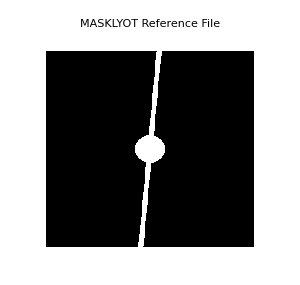
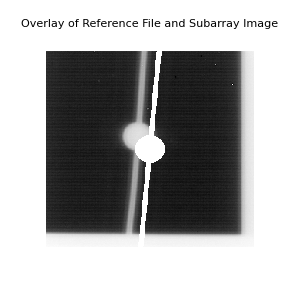
-Graphics--Graphics--Graphics-

```mathematica
Row@{ArrayPlot[illumIms[[k]],DataReversed->True,PlotLabel->Style["Backlit"masks[[k]]"Subarray Image",14],ImageSize->300],ArrayPlot[refs[[k]],DataReversed->True,PlotLabel->Style[ masks[[k]]"Reference File",14],ImageSize->300],ArrayPlot[Normal[refs[[k]]]*Normal[illumIms[[k]]],DataReversed->True,PlotLabel->Style["Overlay of Reference File and Subarray Image",14],ImageSize->300]}
```

```mathematica
lyotFlat=flatData[[k]];
```

```mathematica
Last@lyotFlat//MatrixForm
```

(0 | 1 | DO_NOT_USE | Bad pixel, do not use
1 | 2 | NON_SCIENCE | Non science data
2 | 4 | UNRELIABLE_FLAT | Flat-field variance large
3 | 8 | CDP_PARTIAL_DATA | Data derived from incomplete input
4 | 16 | CDP_LOW_QUAL | Data of low quality
5 | 32 | CDP_UNRELIABLE_ERROR | Data without a reliable error estimate
6 | 64 | NO_FLAT_FIELD | Flatfield value not available
7 | 128 | DIFF_PATTERN | Diffraction & interference patterns)

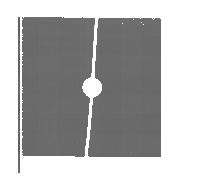
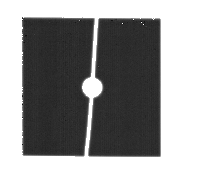
-Graphics- -Graphics- -Graphics-

```mathematica
Row@{ArrayPlot[lyotFlat[[2]],DataReversed->True, ImageSize->200]
ArrayPlot[lyotFlat[[3]],DataReversed->True, ImageSize->200]
ArrayPlot[lyotFlat[[4]], DataReversed->True, ImageSize->200]}
```

```mathematica
dqvals=DeleteDuplicates@Flatten@Normal[lyotFlat[[4]]];
```

```mathematica
normFlat=Normal[lyotFlat[[4]]]/.{Max@dqvals->0,Min@dqvals->1};(*Normalize*)
finFlat=Floor@MedianFilter[normFlat,1]; (*Denoise*)
```

```mathematica
Row@{ArrayPlot[normFlat,DataReversed->True,PlotLabel->Style["Normalized Flat",18],ImageSize->200],
ArrayPlot[finFlat,DataReversed->True,PlotLabel->Style["Noiseless Flat",18],ImageSize->200]}
```

-Graphics--Graphics-

```mathematica
dims=finFlat//Dimensions
```

{304,320}

```mathematica
x1=10;
x2=30;
y1=20;
y2=40;
```

```mathematica
(*This Manipulate function is used to move the mask around to match the correspionding flat file*)
moveMax=100;
Manipulate[
priorMask=1- MakeAperture[r,dims[[1]],dims[[2]]]; (*prior to alignment*)
finMask =Transpose[RotateLeft[Transpose[RotateLeft[priorMask,posX]],posY]];
(*psfmask aligned with subarray*)

finMask[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finMask[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finMask[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finMask[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];
(*finres[[168,145]]=1;*)

figs={finMask,finFlat,finMask*finFlat};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,20},1,50,1},{{posX,-6},-50,50,1},{{posY,16},-50,50,1},{{fignum,1},1,3,1},
{{x1,34},1,moveMax,1},{{x2,2},1,moveMax,1},{{y1,9},1,moveMax,1},{{y2,42},1,moveMax,1}]
```

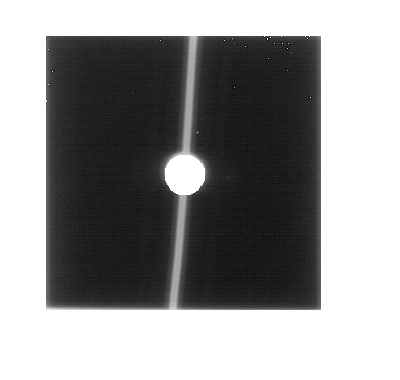

```mathematica
ArrayPlot[finMask*Normal[illumIms[[4]]],DataReversed->True]
```

```mathematica
(*here we export the new mask file*)
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_pre.fits";
Export[expdir,finMask]
```

/Users/bnickson/GitHub/Gen_PSFMASK_ref_files/psf_masks_new/mathematica_out/jwst_miri_psfmask_0004_pre.fits

## MASK1065

1

MIRIM_MASK1065

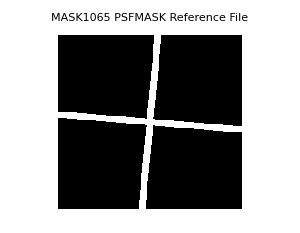
-Graphics--Graphics-

MIRIM_MASK1065

-Graphics--Graphics-

{-2147483582,-2147483648}

```mathematica
k=kass["MIRIM_MASK1065"]
Print[apers[[k]]]
Row@{ArrayPlot[illumIms[[k]],DataReversed->True, PlotLabel->Style["Backlit"masks[[k]]"Subarray Image",14],ImageSize->300],
ArrayPlot[refs[[k]],DataReversed->True, PlotLabel->Style[masks[[k]]"PSFMASK Reference File",14],ImageSize->300]}
```

4

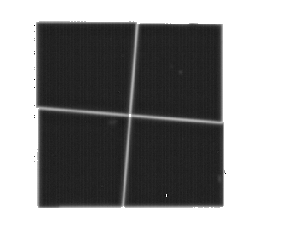
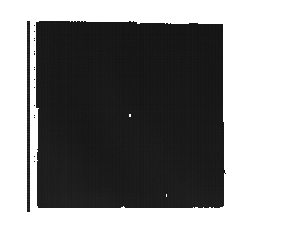
-Graphics--Graphics--Graphics-

```mathematica
flat1065=flatData[[k]];
dqvals=DeleteDuplicates@Flatten@Normal[flat1065[[4]]];
normFlat=Normal[flat1065[[4]]]/.{Max@dqvals->0,Min@dqvals->1};(*Normalize*)
IWA= IWAS[[k]];
initR=Ceiling[IWA/pixelScale]

Row@{ArrayPlot[flat1065[[2]],DataReversed->True,ImageSize->300],
ArrayPlot[flat1065[[3]],DataReversed->True, ImageSize->300],
ArrayPlot[normFlat,DataReversed->True, ImageSize->300]}
```

```mathematica
dims=Dimensions@normFlat
Manipulate[
priorMask = 1-MakeAperture[r,dims[[1]],dims[[2]]]; 
shiftMask=Transpose[RotateLeft[Transpose[RotateLeft[priorMask,posX]],posY]];
(*finres[[168,145]]=1;*)
finMask=shiftMask*Floor@MedianFilter[normFlat,1];

finMask[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finMask[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finMask[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finMask[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];

figs={shiftMask,normFlat,shiftMask*normFlat,finMask};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,initR},1,50,1},{{posX,31},-50,50,1},{{posY,23},-50,50,1},{{fignum,4},1,4,1},
{{x1,7},1,moveMax,1},{{x2,4},1,moveMax,1},{{y1,14},1,moveMax,1},{{y2,60},1,moveMax,1}]
```

{224,288}

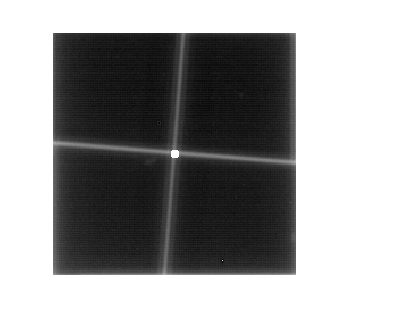

```mathematica
ArrayPlot[Normal[finMask]*Normal[illumIms[[k]]],DataReversed->True]
```

```mathematica
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_pre.fits";
Export[expdir,finMask]
```

/Users/bnickson/GitHub/Gen_PSFMASK_ref_files/psf_masks_new/mathematica_out/jwst_miri_psfmask_0001_pre.fits

```mathematica
(*{{posX,-2},-50,50,1},{{posY,23},-50,50,1},{{n,1},0,10,1}*)
```

## MASK1550

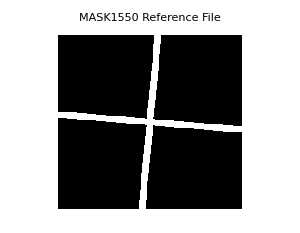
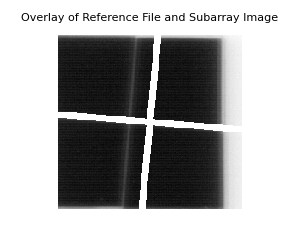
-Graphics--Graphics--Graphics-

```mathematica
k=kass["MIRIM_MASK1550"];
Row@{ArrayPlot[illumIms[[k]],DataReversed->True,PlotLabel->Style["Backlit"masks[[k]]"Subarray Image",14],ImageSize->300],ArrayPlot[refs[[k]],DataReversed->True,PlotLabel->Style[ masks[[k]]"Reference File",14],ImageSize->300],ArrayPlot[Normal[refs[[k]]]*Normal[illumIms[[k]]],DataReversed->True,PlotLabel->Style["Overlay of Reference File and Subarray Image",14],ImageSize->300]}
```

```mathematica
flat1550=flatData[[k]];
dqvals=DeleteDuplicates@Flatten@Normal[flat1550[[4]]];
normFlat=Normal[flat1550[[4]]]/.{Max@dqvals->0,Min@dqvals->1};(*Normalize*)
DeleteDuplicates@Flatten@normFlat
IWA= IWAS[[k]]
initR=Ceiling[IWA/pixelScale]

Row@{ArrayPlot[flat1550[[2]],DataReversed->True, ImageSize->300],
ArrayPlot[flat1550[[3]],DataReversed->True, ImageSize->300],
ArrayPlot[normFlat,DataReversed->True, ImageSize->300]}
```

{0,1}

0.49

5

-Graphics--Graphics--Graphics-

0.49

```mathematica
dims=Dimensions@normFlat;
Manipulate[
priorMask = 1-MakeAperture[r,dims[[1]],dims[[2]]];
shiftMask=Transpose[RotateLeft[Transpose[RotateLeft[priorMask,posX]],posY]];
finMask=shiftMask*Floor@MedianFilter[Normal[normFlat],1];

finMask[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finMask[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finMask[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finMask[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];

figs={shiftMask,normFlat,shiftMask*normFlat,finMask};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,initR},1,50,1},{{posX,35},-50,50,1},{{posY,24},-50,50,1},{{fignum,4},1,4,1},
{{x1,4},1,moveMax,1},{{x2,12},1,moveMax,1},{{y1,13},1,moveMax,1},{{y2,61},1,moveMax,1}]
```

```mathematica
ArrayPlot[finMask * Normal[illumIms[[k]]],DataReversed->True]
```

-Graphics-

```mathematica
Manipulate[ListLinePlot[finMask[[k]]],{{k,114},1,320,1}]
```

```mathematica
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_pre.fits";
Export[expdir,finMask]
```

/Users/bnickson/GitHub/Gen_PSFMASK_ref_files/psf_masks_new/mathematica_out/jwst_miri_psfmask_0002_pre.fits

```mathematica
(*{{posX,-2},-50,50,1},{{posY,23},-50,50,1},{{n,1},0,10,1}*)
```

## MASK1140

```mathematica
k=kass["MIRIM_MASK1140"];
Row@{ArrayPlot[illumIms[[k]],DataReversed->True,PlotLabel->Style["Backlit"masks[[k]]"Subarray Image",14],ImageSize->300],ArrayPlot[refs[[k]],DataReversed->True,PlotLabel->Style[ masks[[k]]"Reference File",14],ImageSize->300],ArrayPlot[Normal[refs[[k]]]*Normal[illumIms[[k]]],DataReversed->True,PlotLabel->Style["Overlay of Reference File and Subarray Image",14],ImageSize->300]}
```

-Graphics--Graphics--Graphics-

```mathematica
flat1140=flatData[[k]];
dqvals=DeleteDuplicates@Flatten@Normal[flat1140[[4]]];
normFlat=Normal[flat1140[[4]]]/.{Max@dqvals->0,Min@dqvals->1};(*Normalize*)
DeleteDuplicates@Flatten@Normal[normFlat]
IWA= IWAS[[k]];
initR=Ceiling[IWA/pixelScale]

Row@{ArrayPlot[flat1140[[2]],DataReversed->True, ImageSize->300],
ArrayPlot[flat1140[[3]],DataReversed->True, ImageSize->300],
ArrayPlot[normFlat,DataReversed->True, ImageSize->300]}
```

{0,1}

4

-Graphics--Graphics--Graphics-

```mathematica
dims=Dimensions@Normal[normFlat];
Manipulate[
priorMask = 1-MakeAperture[r,dims[[1]],dims[[2]]];
shiftMask=Transpose[RotateLeft[Transpose[RotateLeft[priorMask,posX]],posY]];
finMask=shiftMask*Floor@MedianFilter[Normal[normFlat],1];

finMask[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finMask[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finMask[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finMask[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];
figs={shiftMask,normFlat,shiftMask*normFlat,finMask};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,initR},1,50,1},{{posX,34},-50,50,1},{{posY,24},-50,50,1},{{fignum,4},1,4,1},
{{x1,5},1,moveMax,1},{{x2,9},1,moveMax,1},{{y1,13},1,moveMax,1},{{y2,60},1,moveMax,1}]
```

```mathematica
ArrayPlot[Normal[finMask]*Normal[illumIms[[k]]],DataReversed->True]
```

-Graphics-

```mathematica
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_pre.fits";
Export[expdir,finMask]
```

/Users/bnickson/GitHub/Gen_PSFMASK_ref_files/psf_masks_new/mathematica_out/jwst_miri_psfmask_0003_pre.fits